```mathematica
Histogram3D
```

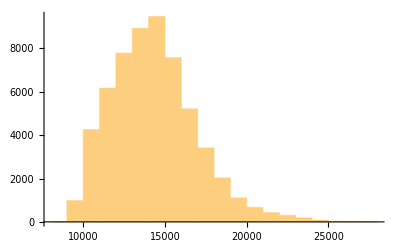

```mathematica
Histogram[loadTimeSeriesResampled]
```

```mathematica
meanMonthlyLoad=TimeSeriesAggregate[loadTimeSeriesResampled,"Month",Mean]
```

TimeSeries[…]

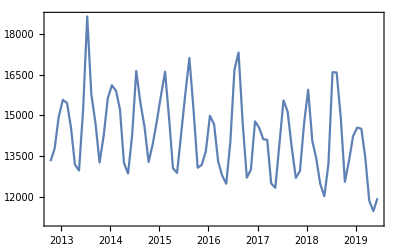

```mathematica
DateListPlot[meanMonthlyLoad]
```

```mathematica
maxMonthlyLoad=TimeSeriesAggregate[loadTimeSeriesResampled,"Month",Max]
```

TimeSeries[…]

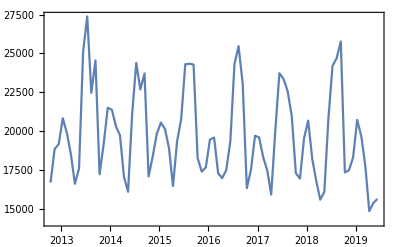

```mathematica
DateListPlot[maxMonthlyLoad]
```

```mathematica
meanQuarterlyLoad=TimeSeriesAggregate[loadTimeSeriesResampled,"Quarter",Mean]
```

TimeSeries[…]

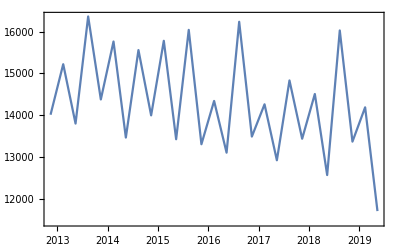

```mathematica
DateListPlot[meanQuarterlyLoad]
```

```mathematica
maxQuarterlyLoad=TimeSeriesAggregate[loadTimeSeriesResampled,"Quarter",Max]
```

TimeSeries[…]

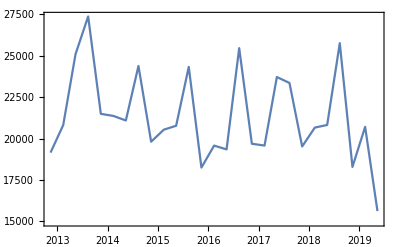

```mathematica
DateListPlot[maxQuarterlyLoad]
```